#### Step 1 : let’s define our prior as a Gamma distribution

Please note that we have two way to define a Gamma distribution

```mathematica
-Graphics-
-Graphics-
```

Note that

Mathematica automatically assumes the (k, θ) methods.
However, in Bayesian statistics, we prefer the (α, β) way. 
Hence, the parameters will be

```mathematica
-Graphics-
-Graphics-
```

based on the parameter values, we define the prior as a function of λ

```mathematica
prior[λ_]:=PDF[GammaDistribution[7,1/5],λ]
```

let' s print its analytic form to see whether it works

```mathematica
prior[λ]
```

Piecewise[{{15625/144 ⅇ^(-5 λ) λ^6, λ>0}, {0, True}}]

let' s plot it as well

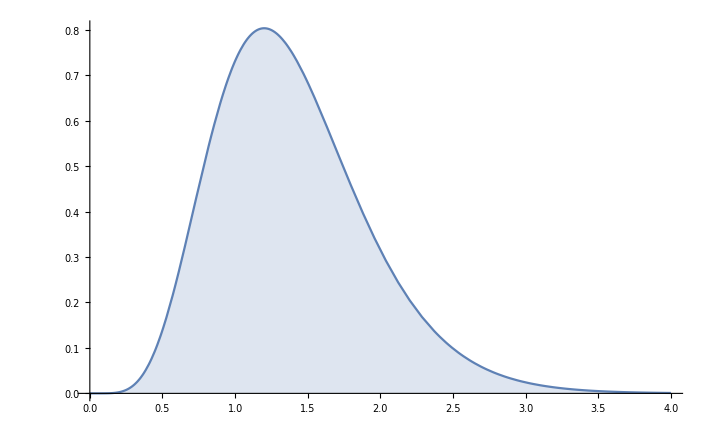

```mathematica
Plot[prior[λ],{λ,0,4},Filling->Axis]
```

#### Step 2 : let’s define our likelihood function of each data point as an Exponential Distribution

```mathematica
lf[x_]:=PDF[ExponentialDistribution[λ],x]
```

```mathematica
lf[x]
```

Piecewise[{{ⅇ^(-x λ) λ, x≥0}, {0, True}}]

```mathematica
Plot[Table[lf[x],{λ,{0.5,1}}]//Evaluate,{x,0,5},Filling->Axis]
```

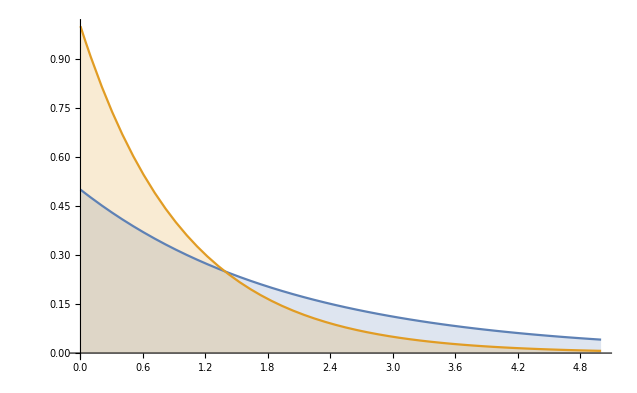

#### Step 3 : let’s define our likelihood function of all data points as the product of Exponential PDFs

```mathematica
likelihood[f_,data_]:=Product[PDF[f,x],{x,data}]
```

```mathematica
likelihood[ExponentialDistribution[λ],{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5]}]
```

(Piecewise[{{ⅇ^(-λ a_1) λ, a_1≥0}, {0, True}}]) (Piecewise[{{ⅇ^(-λ a_2) λ, a_2≥0}, {0, True}}]) (Piecewise[{{ⅇ^(-λ a_3) λ, a_3≥0}, {0, True}}]) (Piecewise[{{ⅇ^(-λ a_4) λ, a_4≥0}, {0, True}}]) (Piecewise[{{ⅇ^(-λ a_5) λ, a_5≥0}, {0, True}}])

```mathematica
l = Simplify[likelihood[ExponentialDistribution[λ],{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5]}]]
```

Piecewise[{{ⅇ^(-λ (a_1+a_2+a_3+a_4+a_5)) λ^5, a_1≥0&&a_2≥0&&a_3≥0&&a_4≥0&&a_5≥0}, {0, True}}]

```mathematica
likelihood[ExponentialDistribution[λ],{1,2,3,4,5}]
```

ⅇ^(-15 λ) λ^5

#### Step 4 : let’s calculate our posterior using Bayes Rule

The Bayes Rule suggests that

Since the denominator is just a constant, we just need to focus on the numerator calculation as follows

```mathematica
num = Simplify[l * prior[λ]]
```

Piecewise[{{15625/144 ⅇ^(-λ (5+a_1+a_2+a_3+a_4+a_5)) λ^11, a_1≥0&&a_2≥0&&a_3≥0&&a_4≥0&&a_5≥0&&λ>0}, {0, True}}]

It looks like a Gamma distribution, which is

Let’s vary our sample points (add one extra sample points) to find the pattern of Gamma paratmeter.

```mathematica
l = Simplify[likelihood[ExponentialDistribution[λ],{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5],Subscript[a, 6]}]];
num = Simplify[l * prior[λ]]
```

Piecewise[{{15625/144 ⅇ^(-λ (5+a_1+a_2+a_3+a_4+a_5+a_6)) λ^12, λ>0&&a_1≥0&&a_2≥0&&a_3≥0&&a_4≥0&&a_5≥0&&a_6≥0}, {0, True}}]

Still a Gamma distribution
Again, let’s vary our sample points (add one extra sample points) to find the pattern of Gamma paratmeter.

```mathematica
l = Simplify[likelihood[ExponentialDistribution[λ],{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5],Subscript[a, 6],Subscript[a, 7]}]];
num = Simplify[l * prior[λ]]
```

Piecewise[{{15625/144 ⅇ^(-λ (5+a_1+a_2+a_3+a_4+a_5+a_6+a_7)) λ^13, λ>0&&a_1≥0&&a_2≥0&&a_3≥0&&a_4≥0&&a_5≥0&&a_6≥0&&a_7≥0}, {0, True}}]

Now we can find the pattern of Gamma paratmeter: